# cutoffs - varying T

## fix σ; calculate <g|ρ|g> for ε = 10Ω; plot as a function of T, the time for which switching is constant

## parameters

```mathematica
α=1;
Ω=1;
ε=10 Ω;
```

```mathematica
numSteps=7;
TMin=1/Ω;TMax=8/Ω; TStepSize=Abs[TMin-TMax]/numSteps;
TValues=Table[T,{T,TMin,TMax,TStepSize}];
```

```mathematica
TValues
```

{1,2,3,4,5,6,7,8}

```mathematica
maxRec=15;
precGoal=10;
workPrec=25;
```

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
(*chiT1[t_,T_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_,T_]:=1/(r+T)
chiT3[t_,T_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])*)
```

```mathematica
chiT1[t_,r_,T_]:=1/(r+T) 1/2*(1+Cos[π/r (t+T/2)])
chiT2[t_,r_,T_]:=1/(r+T)
chiT3[t_,r_,T_]:=1/(r+T) 1/2*(1+Cos[π/r (t-T/2)])
```

```mathematica
(*chicos[t_,T_,r_]:=Piecewise[{{chiT1[t,T,r], -T/2-r≤t<-T/2}, {chiT2[t,T,r], -T/2≤t≤T/2}, {chiT3[t,T,r], T/2<t≤T/2+r}}]*)
```

```mathematica
(*Plot[chicos[t,2,1],{t,-2,2}]*)
```

```mathematica
(*r=.;t=.;*)
```

```mathematica
(*Integrate[chicos[t,T,r],{t,-T/2-r,T/2+r},Assumptions->r∈Reals&&Τ∈Reals&&r>0&&T>0]*)
```

## k integrand

### the first interval

```mathematica
(*tpInt1[t_?NumericQ,k_?NumericQ,T_?NumericQ]:=tpInt1[t,k,T]=NIntegrate[chiT1[tp,T]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2-r,t}]*)
```

```mathematica
(*tInt1[k_?NumericQ,T_?NumericQ]:=tInt1[k,T]=α*NIntegrate[chiT1[t,T] tpInt1[t,k],
{t,-T/2-r,-T/2}]*)
```

### the second interval

```mathematica
(*tpInt2[t_,k_,T_]:=Integrate[chiT2[tp,T]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2,t}]*)
```

```mathematica
(*tInt2[k_,T_]:=α*Integrate[chiT2[t,T] tpInt2[t,k],
{t,-T/2,T/2}]*)
```

### the third interval

```mathematica
(*tpInt3[t_?NumericQ,k_?NumericQ,T_?NumericQ]:=tpInt3[t,k,T]=NIntegrate[chiT3[tp,T]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T/2,t}]*)
```

```mathematica
(*tInt3[k_?NumericQ,T_?NumericQ]:=tInt3[k,T]=α*NIntegrate[chiT3[t,T] tpInt3[t,k],
{t,T/2,T/2+r}]*)
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
(*kIntegrand[k_,T_]:=-1/π*k*ftil[k]^2*(tInt1[k,T]+tInt2[k,T]+tInt3[k,T])*)
```

### workin on them errors

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ,r_?NumericQ,T_?NumericQ]:= tpInt1[t,k,r,T]=   NIntegrate[chiT1[tp,r,T]* Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2-r,t},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec];
tInt1[ k_?NumericQ,r_?NumericQ,T_?NumericQ]:=             tInt1[k,r,T]=    α*NIntegrate[chiT1[t,r,T]*  tpInt1[t,k,r,T],{t,-T/2-r,-T/2},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec];
tpInt2[t_?NumericQ,k_?NumericQ,r_?NumericQ,T_?NumericQ]:= tpInt2[t,k,r,T]=   NIntegrate[chiT2[tp,r,T]* Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2,t},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec];
tInt2[ k_?NumericQ,r_?NumericQ,T_?NumericQ]:=             tInt2[k,r,T]=    α*NIntegrate[chiT2[t,r,T]*  tpInt2[t,k,r,T],{t,-T/2,T/2},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec];
tpInt3[t_?NumericQ,k_?NumericQ,r_?NumericQ,T_?NumericQ]:= tpInt3[t,k,r,T]=   NIntegrate[chiT3[tp,r,T]* Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T,t},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec];
tInt3[ k_?NumericQ,r_?NumericQ,T_?NumericQ]:=             tInt3[k,r,T]=    α*NIntegrate[chiT3[t,r,T]*  tpInt3[t,k,r,T],{t,T/2,T/2+r},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec];

(*the integrand we really want*)
kIntegrand[k_,r_,T_]:=-(1/π)*k*ftil[k]^2*(tInt1[k,r,T]+tInt2[k,r,T]+tInt3[k,r,T])
```

## cutoff functions

```mathematica
gaussianCutoff[k_]:=ⅇ^((-Abs[k]^2)/(2 ε^2));
lorentzianCutoff[k_]:=ε^2/(Abs[k]^2+ε^2);
expCutoff[k_]:=ⅇ^((-Abs[k])/(2 ε));
sharpCutoff[k_]:=HeavisideTheta[k+ε,-k+ε];
```

## <g|ρ|g>

```mathematica
r=0.2;λ=0.1;
```

```mathematica
pGauss=Table[α+λ^2*NIntegrate[gaussianCutoff[k]*kIntegrand[k,r,T],{k,0,∞}],{T,TMin,TMax,TStepSize}]
```

{0.992484,0.996827,0.998047,0.998586,0.99889,0.999088,0.999228,0.999331}

```mathematica
pLor=Monitor[Table[α+λ^2*NIntegrate[lorentzianCutoff[k]*kIntegrand[k,r,T],{k,0,∞}],{T,TMin,TMax,TStepSize}],T]
```

$Aborted

```mathematica
λ=0.1;
```

```mathematica
pSharp=Table[α+λ^2*NIntegrate[kIntegrand[k,r,T],{k,0,ε},MaxRecursion->maxRec, PrecisionGoal->precGoal, WorkingPrecision->workPrec],{T,TMin,TMax,TStepSize}]
```

{0.992434,0.996863,0.998065,0.998587,0.998894,0.999087,0.999227,0.999331}

```mathematica
pExp=Table[α+λ^2*NIntegrate[expCutoff[k]*kIntegrand[k,r,T],{k,0,∞},MaxRecursion->maxRec, PrecisionGoal->precGoal,  WorkingPrecision->workPrec],{T,TMin,TMax,TStepSize}]
```

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
dataGauss=Transpose[{TValues,pGauss}];
dataLor=Transpose[{TValues,pLor}];
dataSharp=Transpose[{TValues,pSharp}];
dataExp=Transpose[{TValues,pExp}];
```

NIntegrate::inumr: The integrand -100\ ⅇ^-k^2/200000000\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π\ (100 + Abs[k]^2)
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -ⅇ^-k^2/200000000\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 10}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -ⅇ^-k^2/200000000 - Abs[k]/20\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -100\ ⅇ^-k^2/200000000\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π\ (100 + Abs[k]^2)
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

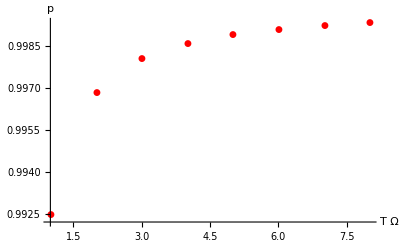

```mathematica
ListPlot[{dataGauss,dataLor,dataSharp,dataExp},
AxesLabel->{T Ω,p},
PlotStyle->{Red,Blue,Green,Black},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pGaussvT.csv",dataGauss];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLorvT.csv",dataLor];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pSharpvT.csv",dataSharp];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pExpvT.csv",dataExp];
```

NIntegrate::inumr: The integrand -100\ ⅇ^-k^2/200000000\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π\ (100 + Abs[k]^2)
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -ⅇ^-k^2/200000000\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 10}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand -ⅇ^-k^2/200000000 - Abs[k]/20\ k\ (∫_-T/2 T/2 tpInt2[t, k]/0.2  + T ⅆ t + tInt1[k, T] + tInt3[k, T])/π
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.